Nick G. Toth
Jan 15, 2020
Math 351
Assignment 2

Exercise 1.20

What is the fifth term in the Taylor Series for (1-2h)^(1/2)?

As we calculated in the first homework assignment, (1+x)^(1/2) = 1+ ∑_(k=1)^∞ ((-1)^(k+1)F(k-2))/(k!2^k)(x)^k .
(1-2h)^(1/2) is just (1+x)^(1/2) composed with -2h, so we have
            (1-2h)^(1/2)=  1+ ∑_(k=1)^∞ ((-1)^(k+1)F(k-2))/(k!2^k)(-2h)^k , where F(L) = ∏ _(k=0)^L (2 k+1).

In this case, we want to take the fourth term in the sum, since the series begins with 1.
i.e. The solution is obtained by evaluating((-1)^(k+1)F(k-2))/(k!2^k)(-2h)^kfor k=4.

((-1)^(4+1)F(4-2))/(4!2^4)(-2h)^4 = -15/(4!)h^4.

Exercise 1.22

Show how p(x) = 6*(x+3) + 9*(x+3)^5- 5*(x+3)^8 - (x+3)^11can be efficiently evaluated.

Note that I will assume the computation of x^k is equivalent to k-1 multiplications

Also note that the direct computation of p(x) requires 7 additions, 24 multiplications, and 4 memory reads.

Now suppose we first compute α = x+3.
Then we can write
p(x) = 6α + 9α^5- 5α^8 - α^11
         = α (6+ 9α^4- 5α^7 - α^10)
         = α (6+ α^4(9- 5α^3 - α^6))
         = α (6+ α^4(9- α^3(5 + α^3)))

Now compute and β = α^3.
Then we can write
p(x) = α (6 + βα(9 - β(5 + β)))

Observe that we could just as easily have computed β=α^3 at the same time that we computed α = x+3.
Thence follows the following efficient implementation of the polynomial:

                First compute α  =  x+3 and β=α^3.
                Now return  α *(6 + β*α*(9 - β*(5 + β)))

This method requires 4 additions, 6 multiplications, 2 memory writes, and 9 memory reads.

After testing both methods in c++, it is clear that the method derived here is considerably more efficient than
direct computation. In fact, the second method consistently ran in 20% of the time of the direct computation.

Exercise 1.30

Use Taylor’s Theorem to find a linear function that approximates cos(x) best in the vicinity of x=(5π)/6.

The first derivative of cos(x) is -sin(x), so the slope of the tangent line will be -sin(x) at x=(5π)/6, i.e. -sin((5π)/6) = -1/2.
The tangent line is centered at x=(5π)/6, so it will have the form -1/2(x-(5π)/6) + C for some C.
Now we need to translate the line along the y axis so that it is tangent to cos(x) at x=(5π)/6. i.e. C=cos((5π)/6) = -(√3)/2.

Finally we have arrived at the linear approximation - 1/2((x-(5π)/6)+√3).

Exercise 3.1

Find where the graphs of  y=3x and y=e^x intersect by finding roots of e^x - 3x = 0 correct to four decimal places.

e^x - 3x = 0 has two roots at approximately x = 0.62 and x = 1.51

Lets compute the smaller root by performing the bisection method on the interval [0.61, 0.63].

x_0 = (a_0+b_0)/2 = (0.61+0.63)/2 =  0.62,                              f(b_0)f(0.62) > 0, so a_1 = a_0 and b_1 = x_0,
x_1 = (a_1+b_1)/2=(0.61+0.62)/2 =  0.615,                              f(0.61)f(0.615) > 0, so a_2 = 0.615 and b_2= 0.62,
x_2 = (a_2+b_2)/2=(0.615+0.62)/2 =  0.6175,                          f(0.615)f(0.6175) > 0, so a_3 = 0.6175 and b_3= 0.62,
x_3 = (a_3+b_3)/2=(0.6175+0.62)/2 =  0.61875,                      f(0.6175)f(0.61875) > 0, so a_4 = 0.61875 and b_4= 0.62,
x_4 = (a_4+b_4)/2=(0.61875+0.62)/2 =  0.619375,                  f(0.62)f(0.619375) > 0, so a_5 = 0.619375 and b_5= 0.61875,
x_5 = (a_5+b_5)/2=(0.619375+0.61875)/2 =  0.6190625,        f(0.6190625) = 0.000001 <  0.0001.

So the first root is approximately 0.61906

Next we will compute the larger root by performing the bisection method on the interval [1.5, 1.52].

Now we apply the algorithm:
x_0 = (a_0+b_0)/2 = (1.5+1.52)/2= 1.51,                               f(1.5)f(1.51) > 0, so a_1 = 1.51 and b_1 = 1.52,
x_1 = (a_1+b_1)/2 = (1.51+1.52)/2= 1.515,                           f(1.52)f(1.515) > 0, so a_1 = 1.51 and b_1 = 1.515,
x_2 = (a_2+b_2)/2 = (1.51+1.515)/2= 1.5125,                       f(1.515)f(1.5125) > 0, so a_1 = 1.51 and b_1 = 1.5125,
x_3 = (a_3+b_3)/2 = (1.51+1.5125)/2= 1.51125,                   f(1.51)f(1.51125) > 0, so a_1 = 1.51125 and b_1 = 1.5125,
x_4 = (a_4+b_4)/2 = (1.51125+1.5125)/2= 1.511875,            f(1.5125)f(1.5125) > 0, so a_1 = 1.511875 and b_1 = 1.5125,
x_5 = (a_5+b_5)/2 = (1.511875+1.5125)/2= 1.5121875,        f(1.5121875) = 0.00008 < 0.0001.

So the second root is approximately 1.51218

Exercise 3.2

Give a graphical demonstration that the equation tan x = x has infinitely many roots. Determine one root precisely and another approximately by using a graph. Hint: Use the approach of the preceding problem.

Tan(x) = x can be written as (sin(x))/(cos(x))=x, which gives us the equation sin(x)-xcos(x)=0.
So Tan(x) = x has infinitely many  solutions if and only if  sin(x)-xcos(x)=0 has infinitely many solutions.

Now observe the graph of sin(x)-xcos(x)

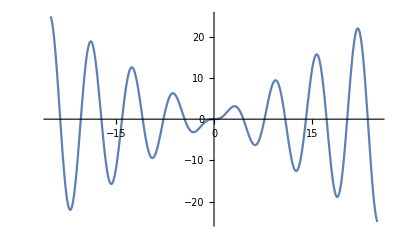

```mathematica
Plot[Sin[x]-x*Cos[x],{x,-25,25}]
```

If that’s not enough to convince you, consider that sin(nπ ) = 0 for all integers n, and cos(nπ ) = 1 when n is even and cos(nπ ) = -1 when n is odd. So sin(nπ)-nπcos(nπ) = -nπ cos(nπ) = -nπ  when n is even, and nπ  when n is odd. 

Now note that the derivative of sin(x)-xcos(x) is cos(x)-(cos(x)-xsin(x)) = xsin(x).
We already showed that xsin(x) = 0 whenever x = nπ for some integer n, so we know that x=nπ is always an extremum of sin(x)-xcos(x).

Coupling the last fact with the property that the sign of -nπ cos(nπ) alternates, and the property that sin(x)-xcos(x) is continuous by the algebraic limit theorem, we can conclude by the intermediate value theorem that 
sin(x)-xcos(x) has a zero in any interval of the form ((n-1)π , nπ) for n in {..., -3, -2, -1, 2, 3, ...}.
These intervals are disjoint subsets of the real numbers, and there are infinitely many integers elements of  {..., -3, -2, -1, 2, 3, ...}, so there are infinitely many real solutions to sin(x)-xcos(x).

The only excluded root in the method described above, and the only root which we will consider exactly
is x=0. We didn’t consider x=0 before, since it is contained in neither (-π , 0) nor (0 , π) (although it is the only point in the intersection of the boundary of these intervals). It is also trivial to compute, since sin(0) = 0. i.e.
sin(0)-0cos(0) = 0.

Now look more closely at the graph, and discover that x=4.5 is roughly a solution to sin(x)-xcos(x).

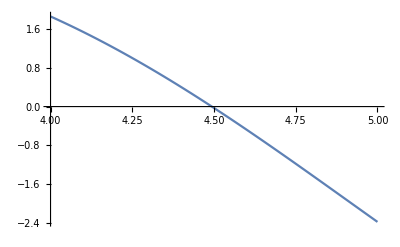

```mathematica
Plot[Sin[x]-x*Cos[x],{x,4,5}]
```

Exercise 3.8

If a = 0.1 and b=1.0, how many steps of the bisection method are necessary to determine the root with an error bounded by 1/2*10^-8.

By the Bisection Method Theorem, we want n satisfying (b-a)/2^(n+1)<1/2*10^-8.

(b-a)/2^(n+1)<1/2*10^-8 ⟺ 0.9/2^n<10^-8
                            ⟺ 1/2^n<1/(0.9*10^8)
                            ⟺ 2^n>0.9*10^8
                            ⟺ nln(2)>ln(0.9*10^8)
                            ⟺ n>(ln(0.9*10^8))/(ln(2)).

```mathematica
(ln(0.9*10^8))/(ln(2))
```

26.4234

So the smallest integer n satisfying (b-a)/2^(n+1)<1/2*10^-8 is n = 27.